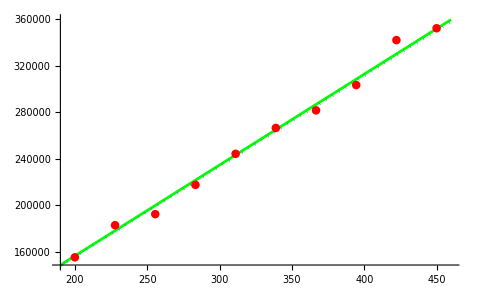

```mathematica
NN = 1000;(*Количество молекул кислорода*)
NT = 10;(*Количество рассматриваемых температур*)
k = 1.38*10^-23;(*Постоянная Больцмана*)
m = 5.32*10^-26;(*Масса одной молекулы О2*)
f[v_,T_] := 4 Pi (m/(2 Pi k T))^(3/2)*v^2*Exp[(-m v^2)/(2 k T)](*Распределение скоростей Максвелла*)
t = Table[200+250/(NT-1)*i,{i,0,NT-1}]; (*Список температур*)
data =Table[RandomVariate[ProbabilityDistribution[f[x,t[[i]]],{x,0,Infinity}],NN],{i,1,NT}]; (*Списки скоростей молекул*)
Histogram[data,Automatic];
vSred = Table[{t[[i]],1/NN*Sum[data[[i,j]]^2,{j,1,NN}]},{i,1,NT}];(*Температуры и средние квадраты скоростей*)
(*Метод наименьших квадратов*)
k1=Sum[vSred[[i,1]]*vSred[[i,2]],{i,1,NT}]/Sum[vSred[[i,1]]^2,{i,1,NT}];
k2 =(3 k)/m; (*Угловой коэффицент из формулы энергии*)
Show[Plot[y = k1*x,{x,190,460},PlotStyle->Green],Plot[y = k2*x,{x,190,460},PlotStyle->Dotted],ListPlot[vSred,PlotStyle->Red]]
```